Oh last day, day 25. My memory deceived me , I expected that we have 30 challenges for 30 days, but no, only 25 challenges, and seem like it end exactly in Christmas

```mathematica
input=;
```

```mathematica
smallInput = ;
```

hum, what kind of this problem, the data look like tree, or graph.Let try to model it, I still have no idea what we should do here.

```mathematica
parseRule=(x↦{x[[1]]-> (StringTrim[x[[2]]]//StringSplit[#," "]&)}) /@ (StringSplit[#,{":",","}]&/@( input//StringSplit[#,"\n"]&));
```

```mathematica
parseRule//Short
```

{{hgm→{krj,psx,xsl,bpt}},{pgz→{mhs,rsb,mvk,jjz}},«1211»,{trh→{vql,jxj}}}

```mathematica
convertDiagramToRules[diagram_List]:=Module[{
key = Keys@@diagram,
values = Values@@diagram
},
key <-> # & /@ values
]
```

```mathematica
graphRules = convertDiagramToRules[#]&/@ parseRule//Flatten;
graphRules//Short
```

{hgm<->krj,hgm<->psx,hgm<->xsl,hgm<->bpt,«3306»,jmd<->rxv,jmd<->djj,trh<->vql,trh<->jxj}

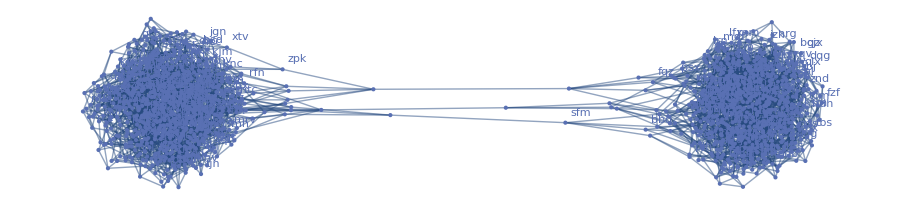

```mathematica
graph = Graph[graphRules,VertexLabels->Automatic]
```

Oh well, just look at the graph, we will see 3 pair need to cut is {mfc,vph},{rmg,fql},{vmt,sfm}, it a bit hard to see, we need test it

remove those guessed edges

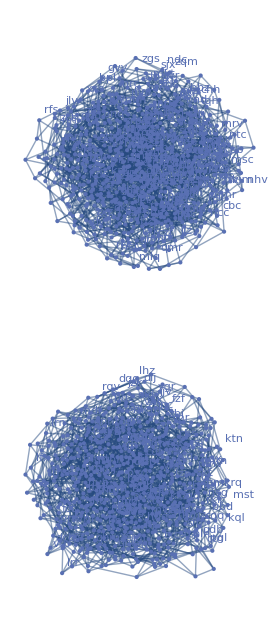

```mathematica
disconnectedGraph = EdgeDelete[graph,{"mfc" <-> "vph","rmg"<->"fql","vmt"<->"sfm"}]
```

Oh, good good

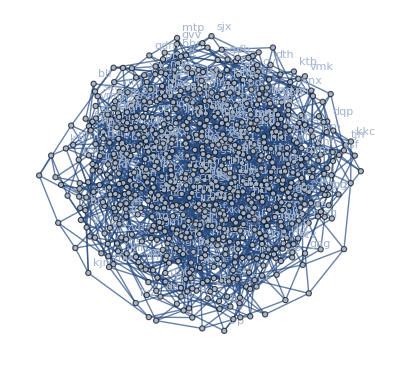
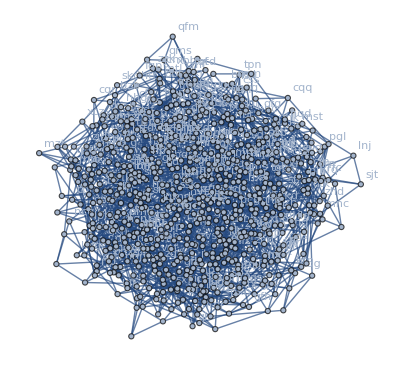

```mathematica
{g1,g2}=ConnectedGraphComponents[disconnectedGraph]
```

```mathematica
VertexCount/@ {g1,g2}/. List -> Times
```

551196

Oh my gosh, Wolfram language so powerful, I don' t even need implement the algorithm for my own

## Scratchpad

```mathematica
SetDirectory["~/nhannht-projects/aoc2023"];
```

```mathematica
NotebookSave[EvaluationNotebook[],FileNameJoin[{Directory[],"25.nb"}]]
```

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
Export[FileNameJoin[{Directory[],"25.pdf"}],EvaluationNotebook[]]
```

/home/vermin/nhannht-projects/aoc2023/25.pdf